```mathematica
Remove["Global`*"]
SetDirectory[NotebookDirectory[]]
```

/Users/elevien/Dropbox (Dartmouth College)/TEACHING/Dartmouth/math23/hw/hw1

### Section 1.1

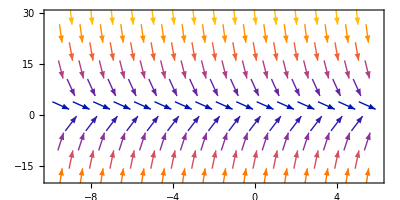

./1p1_1.pdf

```mathematica
p = VectorPlot[{1,3-2 y},{x,-10,6},{y,-19,30},AspectRatio->0.5]
Export["./1p1_1.pdf",p]
```

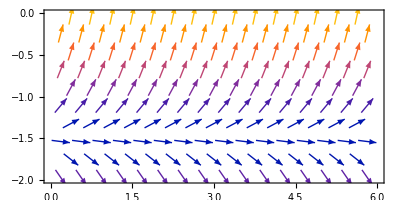

./1p1_3.pdf

```mathematica
p = VectorPlot[{1,3+2 y},{x,0,6},{y,-2,0},AspectRatio->0.5]
Export["./1p1_3.pdf",p]
```

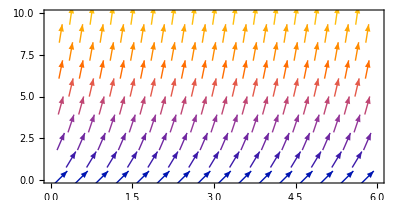

./1p1_3.pdf

```mathematica
p = VectorPlot[{1,3+2 y},{x,0,6},{y,0,10},AspectRatio->0.5]
Export["./1p1_3.pdf",p]
```

```mathematica
D[t^(1/2),{t,2}]
```

-1/(4 t^(3/2))

```mathematica
D[t^-1,{t,2}]
```

2/t^3

```mathematica
DSolve[{r1'[t]== -h r1[t]+h r2[t],r2'[t]== h r1[t]-h r2[t],r1[0]== 0,r2[0]== 1},{r1[t],r2[t]},t]
```

{{r1[t]→1/2 ⅇ^(-2 h t) (-1+ⅇ^(2 h t)),r2[t]→1/2 ⅇ^(-2 h t) (1+ⅇ^(2 h t))}}

```mathematica
DSolve[q'[t]==- h q[t] + h(1-q[t]),q[t],t]
```

{{q[t]→1/2+ⅇ^(-2 h t) C[1]}}

```mathematica
DSolve[{q'[t]==w - (w+k)q[t]},q[t],t]//FullSimplify
```

{{q[t]→w/(k+w)+ⅇ^(-t (k+w)) C[1]}}

```mathematica
3/Log[2]//N
```

4.32809

```mathematica
D[(x^(1-1/a)(x0/(1-x0)(1-x)/x-1))^-a,x]//FullSimplify
```

-(((x^(-1/a) (x-x0))/(-1+x0))^-a ((-1+a) x+x0))/(x (x-x0))

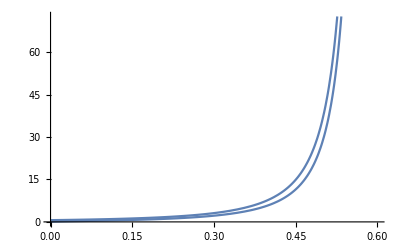

```mathematica
Plot[{-(((x^(-1/a) (x-x0))/(-1+x0))^-a ((-1+a) x+x0))/(x (x-x0)),(a ((x^-a (x-x0))/(-1+x0))^-a ((-1+a) x-a x0))/(x (x-x0))}/.{x0-> 0.6,a-> 1.2},{x,0,0.6}]
```

```mathematica
-(((x^(-1+1/a) (x-x0))/(-1+x0))^-a (x+(-1+a) x0))/(x (x-x0))
```

-(((x^(-1+1/a) (x-x0))/(-1+x0))^-a (x+(-1+a) x0))/(x (x-x0))

```mathematica
Solve[{c ((b+1)/2)==1,(c ((1-b)/2))==(x/(1-x))^w},{c,b}]//FullSimplify
```

{{c→1+(x/(1-x))^w,b→-1+2/(1+(x/(1-x))^w)}}

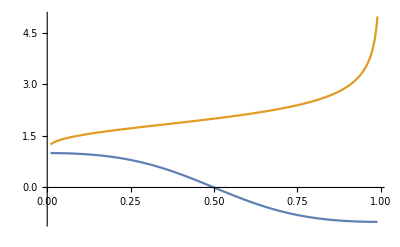

```mathematica
Plot[{-1+2/(1+(x/(1-x))^w)/.{w->2},1+(x/(1-x))^w/.{w->0.3}},{x,0.01,0.99}]
```